# RMSE

Functions

```mathematica
getMomentsTrue[IC_]:=Module[
{m1True,m2True,m3True,m4True,m1Ave,m2Ave,m3Ave,m4Ave},
SetDirectory[NotebookDirectory[]];
Do[
m1True=Transpose[Import["../../bimol_test_stoch_sim/data/ic_v"<>IntegerString[IC,10,3]<>"/lattice_v"<>IntegerString[iLatt,10,3]<>"/counts/A.txt","Table"]][[2]];
m2True=Transpose[Import["../../bimol_test_stoch_sim/data/ic_v"<>IntegerString[IC,10,3]<>"/lattice_v"<>IntegerString[iLatt,10,3]<>"/nns/A_A.txt","Table"]][[2]];
m3True=Transpose[Import["../../bimol_test_stoch_sim/data/ic_v"<>IntegerString[IC,10,3]<>"/lattice_v"<>IntegerString[iLatt,10,3]<>"/triplets/A_A_A.txt","Table"]][[2]];
m4True=Transpose[Import["../../bimol_test_stoch_sim/data/ic_v"<>IntegerString[IC,10,3]<>"/lattice_v"<>IntegerString[iLatt,10,3]<>"/quartics/A_A_A_A.txt","Table"]][[2]];

If[iLatt==1,
m1Ave=m1True;
m2Ave=m2True;
m3Ave=m3True;
m4Ave=m4True;
,
m1Ave+=m1True;
m2Ave+=m2True;
m3Ave+=m3True;
m4Ave+=m4True;
];
,{iLatt,1,49}];

m1Ave/=49.0;
m2Ave/=49.0;
m3Ave/=49.0;
m4Ave/=49.0;

Return[{m1Ave,m2Ave,m3Ave,m4Ave}]
];
```

```mathematica
getMomentsSampled[IC_,str_]:=Module[
{m1,m2,m3,m4},
SetDirectory[NotebookDirectory[]];
m1=Flatten[Import["../data_learned_"<>str<>"/samples/ic_v"<>IntegerString[IC,10,3]<>"_m1.txt","Table"]];
m2=Flatten[Import["../data_learned_"<>str<>"/samples/ic_v"<>IntegerString[IC,10,3]<>"_m2.txt","Table"]];
m3=Flatten[Import["../data_learned_"<>str<>"/samples/ic_v"<>IntegerString[IC,10,3]<>"_m3.txt","Table"]];
m4=Flatten[Import["../data_learned_"<>str<>"/samples/ic_v"<>IntegerString[IC,10,3]<>"_m4.txt","Table"]];
Return[{m1,m2,m3,m4}];
];
```

True moments from stoch sims

### Single

```mathematica
{m1True,m2True,m3True,m4True}=getMomentsTrue[1];
```

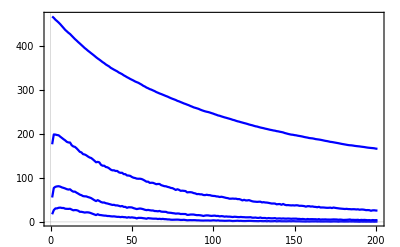

```mathematica
pltTrue=ListLinePlot[{m1True,m2True,m3True,m4True},PlotStyle->Blue]
```

### Map of all true

```mathematica
m1TrueAll=Association[];
m2TrueAll=Association[];m3TrueAll=Association[];m4TrueAll=Association[];
Monitor[
Do[
{m1TrueAll[IC],m2TrueAll[IC],m3TrueAll[IC],m4TrueAll[IC]}=getMomentsTrue[IC];
,{IC,1,49,1}];
,ProgressIndicator[IC,{1,49}]]
```

```mathematica
ICtest=36;
Monitor[
Do[
{m1TrueAll[IC],m2TrueAll[IC],m3TrueAll[IC],m4TrueAll[IC]}=getMomentsTrue[IC];
,{IC,ICtest,ICtest,1}];
,ProgressIndicator[IC,{ICtest,ICtest}]]
```

Sampled moments from visible & hidden models

```mathematica
{m1Vis,m2Vis,m3Vis,m4Vis}=getMomentsSampled[1,"visible"];
{m1Hid,m2Hid,m3Hid,m4Hid}=getMomentsSampled[1,"hidden"];
```

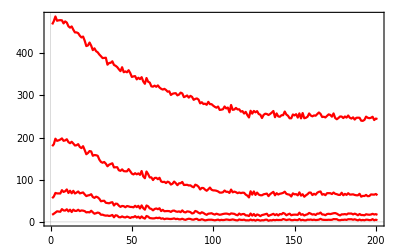

```mathematica
pltVis=ListLinePlot[{m1Vis,m2Vis,m3Vis,m4Vis},PlotStyle->Red]
```

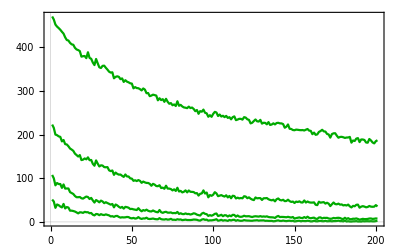

```mathematica
pltHid=ListLinePlot[{m1Hid,m2Hid,m3Hid,m4Hid},PlotStyle->Darker[Green]]
```

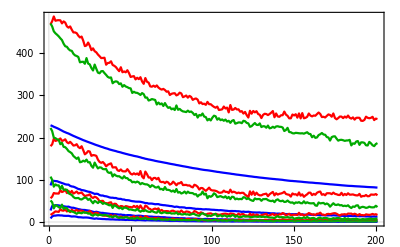

```mathematica
Show[pltTrue,pltVis,pltHid,PlotRange->All]
```

Comparison for single trajectory

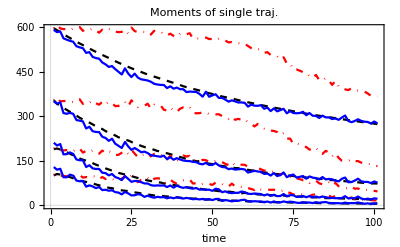

```mathematica
ICtest=36;

{m1Vis,m2Vis,m3Vis,m4Vis}=getMomentsSampled[ICtest,"visible"];
{m1Hid,m2Hid,m3Hid,m4Hid}=getMomentsSampled[ICtest,"hidden"];

pltVis=ListLinePlot[{m1Vis,m2Vis,m3Vis,m4Vis},PlotStyle->{{Red,DotDashed}}];
pltHid=ListLinePlot[{m1Hid,m2Hid,m3Hid,m4Hid},PlotStyle->Blue];
pltTrue=ListLinePlot[{m1TrueAll[ICtest],m2TrueAll[ICtest],m3TrueAll[ICtest],m4TrueAll[ICtest]},PlotStyle->{{Black,Dashed}}];

pltSE=Show[pltTrue,pltVis,pltHid,PlotLabel->"Moments of single traj.",FrameLabel->{"time",""}]
```

```mathematica
pltLeg=LineLegend[{{Black,Dashed},{Red,DotDashed},Blue},{"Stoch. Sim.","Visible Model","Hidden Model"},LabelStyle->{FontSize->20}]
```

Ave square error for single trajectory

```mathematica
getSquareError[sampled_,true_]:=Return[(sampled-true)^2];
```

```mathematica
m1seVis=getSquareError[m1Vis,m1TrueAll[ICtest]];
m2seVis=getSquareError[m2Vis,m2TrueAll[ICtest]];m3seVis=getSquareError[m3Vis,m3TrueAll[ICtest]];m4seVis=getSquareError[m4Vis,m4TrueAll[ICtest]];
m1seHid=getSquareError[m1Hid,m1TrueAll[ICtest]];
m2seHid=getSquareError[m2Hid,m2TrueAll[ICtest]];m3seHid=getSquareError[m3Hid,m3TrueAll[ICtest]];m4seHid=getSquareError[m4Hid,m4TrueAll[ICtest]];
```

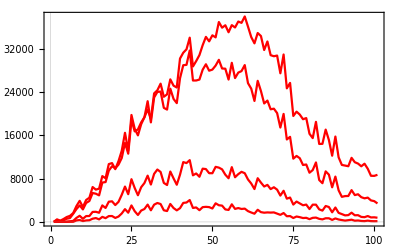

```mathematica
pltseVis=ListLinePlot[{m1seVis,m2seVis,m3seVis,m4seVis},PlotStyle->Red]
```

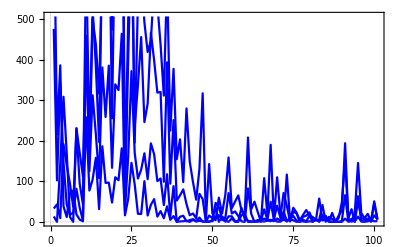

```mathematica
pltseHid=ListLinePlot[{m1seHid,m2seHid,m3seHid,m4seHid},PlotStyle->Blue]
```

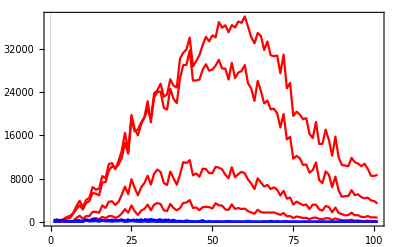

```mathematica
Show[pltseVis,pltseHid]
```

Average error across trajectories

```mathematica
m1seVis=Association[];
m2seVis=Association[];
m3seVis=Association[];
m4seVis=Association[];
m1seHid=Association[];
m2seHid=Association[];
m3seHid=Association[];
m4seHid=Association[];
Do[
{m1Vis,m2Vis,m3Vis,m4Vis}=getMomentsSampled[IC,"visible"];
{m1Hid,m2Hid,m3Hid,m4Hid}=getMomentsSampled[IC,"hidden"];

m1seVis[IC]=getSquareError[m1Vis,m1TrueAll[IC]];
m2seVis[IC]=getSquareError[m2Vis,m2TrueAll[IC]];m3seVis[IC]=getSquareError[m3Vis,m3TrueAll[IC]];m4seVis[IC]=getSquareError[m4Vis,m4TrueAll[IC]];
m1seHid[IC]=getSquareError[m1Hid,m1TrueAll[IC]];
m2seHid[IC]=getSquareError[m2Hid,m2TrueAll[IC]];m3seHid[IC]=getSquareError[m3Hid,m3TrueAll[IC]];m4seHid[IC]=getSquareError[m4Hid,m4TrueAll[IC]];

,{IC,1,49,1}];
```

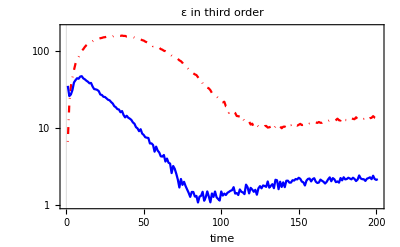

```mathematica
pltm3=ListLogPlot[{Sqrt[Mean[Values[m3seVis]]],Sqrt[Mean[Values[m4seHid]]]},PlotStyle->{{Red,DotDashed},Blue},FrameLabel->{"time",""},PlotLabel->"ε in third order",PlotRange->{1,200}]/.Point->Line
```

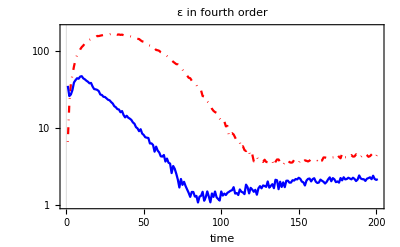

```mathematica
pltm4=ListLogPlot[{Sqrt[Mean[Values[m4seVis]]],Sqrt[Mean[Values[m4seHid]]]},PlotStyle->{{Red,DotDashed},Blue},FrameLabel->{"time",""},PlotLabel->"ε in fourth order",PlotRange->{1,200}]/.Point->Line
```

```mathematica
pltLeg2=LineLegend[{{Red,DotDashed},Blue},{"Visible Model","Hidden Model"},LabelStyle->{FontSize->20}]
```

Figures

```mathematica
SetDirectory[NotebookDirectory[]];
If[!DirectoryQ["../figures"],CreateDirectory["../figures"]];
Export["../figures/mse_ave_m4.pdf",pltm4]
```

../figures/mse_ave_m4.pdf

```mathematica
SetDirectory[NotebookDirectory[]];
If[!DirectoryQ["../figures"],CreateDirectory["../figures"]];
Export["../figures/mse_ave_m3.pdf",pltm3]
```

../figures/mse_ave_m3.pdf

```mathematica
SetDirectory[NotebookDirectory[]];
If[!DirectoryQ["../figures"],CreateDirectory["../figures"]];
Export["../figures/mse_leg_2.pdf",pltLeg2]
```

../figures/mse_leg_2.pdf

LEGACY

```mathematica
trajsHidden=trajs;
```

```mathematica
trajseHid=trajsHidden[[ICtest]];
```

```mathematica
m1seNormHid=m1seHid-Min[m1seHid];
m1seNormHid/=Max[m1seNormHid];
```

```mathematica
cols=ColorData["LightTemperatureMap"][#]&/@m1seNormHid;
```

```mathematica
Graphics3D[Line[trajseHid,VertexColors->cols]]
```

-Graphics3D-

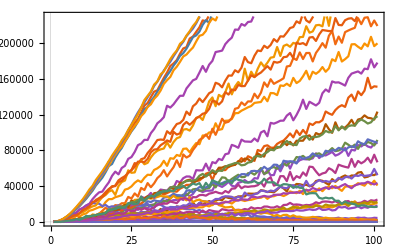

```mathematica
ListLinePlot[Values[m1seVis]]
```

```mathematica
m1minHid =Min[Flatten[Values[m1seHid]]];
m1maxHid =Max[Flatten[Values[m1seHid]]];
m1minVis =Min[Flatten[Values[m1seVis]]];
m1maxVis =Max[Flatten[Values[m1seVis]]];
```

```mathematica
m1seNormVis=Association[];
m1seNormHid=Association[];
Do[
m1seNormVis[IC]=m1seVis[IC]-m1minVis;
m1seNormVis[IC]/=m1maxVis;
m1seNormHid[IC]=m1seHid[IC]-m1minHid;
m1seNormHid[IC]/=m1maxHid;
,{IC,1,50,1}];
```

```mathematica
linesm1Hid={};
linesm1Vis={};
Do[
trajseHid=trajsHidden[[IC]];
trajseVis=trajsVisible[[IC]];

cols=ColorData["LightTemperatureMap"][#]&/@m1seNormHid[IC];
AppendTo[linesm1Hid,Line[trajseHid,VertexColors->cols]];
cols=ColorData["LightTemperatureMap"][#]&/@m1seNormVis[IC];
AppendTo[linesm1Vis,Line[trajseVis,VertexColors->cols]];

,{IC,1,50,1}];
```

```mathematica
Graphics3D[linesm1Hid]
```

-Graphics3D-

```mathematica
Graphics3D[linesm1Vis]
```

-Graphics3D-